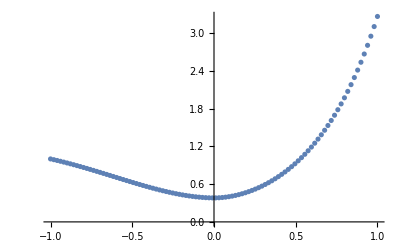

```mathematica
(* Left boundaru condition*)
a=-1;
(* Right boundary condition*)
b=1;
(*Kernel*)
K[ξ_,t_]=Sqrt[ξ^2+t^2];
(*Rhs function*)
f[t_]=t^2;
(* Number on nodes *)
NN = 100;
(*Grid*)
UniformGrid = Table[i,{i,a,b,(b-a)/(NN-1)}]; 
(*Array of uniform weight vector*)
α=Table[0,{NN}];

Dw=Table[0.0,{i,1,NN},{l,1,NN}];
(*Filling matrix Dw*)
For[j=1,j<=NN,j++,
(*Preparation for the natural spline making*)
w=Table[{UniformGrid[[k]],0.0},{k,1,NN}]; (*Pairs of values {grid point, function values}*)
w[[j,2]]=1; (*Definition of natural spline as a spline through only 1 nodes with value 1 and others are 0*)(*Interpolation polynom*)
S=Interpolation[w];
For[i=1,i<NN,i++,
Dw[[i+1,j]]=Dw[[i,j]]+Integrate[S[x],{x,UniformGrid[[i]],UniformGrid[[i+1]]}];
];
];
(*Print["Matrix of weights:"]
MatrixForm[Dw]*)
(*MatrixForm[α]*)
(*Assemble left hand side of SLAE*)
Lhs=Table[0.0
,{i,1,NN},{j,1,NN}] ;
For[i=1,i<=NN,i++,
For[j=1,j<=NN,j++,
m=K[UniformGrid[[j]],UniformGrid[[i]]];
Lhs[[i,j]]=If[i!=j,
-Dw[[i,j]]*m ,(*Condition is True*)
1-Dw[[i,j]]*m(*Condition is False*)
];
];
];
(*Print["Left hand side of the system"]
MatrixForm[Lhs]*)
(*Assemble Right hand side of the SLAE*)
Rhs=Table[0.0,{NN}];
For[i=1,i<=NN,i++,
Rhs[[i]]=f[UniformGrid[[i]]];
];
(*Print["Right hand side of the system"]
MatrixForm[Rhs] //N*)
(*Prepare Solution*)
SolutionOfSLAE = LinearSolve[Lhs,Rhs];
(*Print["Solution of the SLAE"]
MatrixForm[SolutionOfSLAE]*)
FunctionSolution=Table[{UniformGrid[[i]],SolutionOfSLAE[[i]]},{i,1,NN}];
ListPlot[FunctionSolution]
```